# An example needing EFFORT

### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Test

Select a ruleset to investigate, given its reduced rank index, quinary code, or ruleset, giving it some convenient name:

```mathematica
rs01=FromReducedRankIndex[6308190100]
```

<|Index→6308190100,QCode→34243232424233,RuleSet→{AB→BA,AA→B,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:

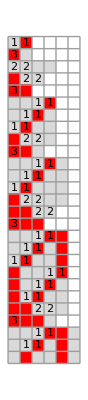



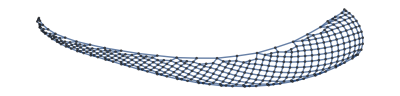
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "AB",800, (* choose an appropriate initial state string, and # steps *)
(* options *) Min->1,Max->400,SSSMin->Automatic,SSSMax->27,NetMin->Automatic,NetMax->384,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];(* options can be changed or omitted, but these are reasonable choices *)
```

Remember the buttons in SSSInteractiveDisplay to use the options you selected either one time or as default:

```mathematica
SSSInteractiveDisplay[sss01]
```

Then we may look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss01[["Net"]]//Short
```

{1→2,2→3,2→3,2→4,1→4,3→5,«1554»,796→797,797→798,796→798,795→799,748→799,755→800}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42},{44},{1,2,3},{1,3},{1,3},{3,45},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,4},{1,2},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.  I don’t believe anything after the last 44.

```mathematica
Position[nds01,44]
```

{{704,1},{708,2},{751,1}}

```mathematica
nds01[[1;;750]]
```

{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44},{1,2,3},{1,3},{1,3},{3,44},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,3},{1,3},{3,42},{1,51},{1,2},{1,42}}

Try the reduction:

```mathematica
rsl01=ReduceSetList[nds01[[1;;750]]]
```

{{1,3},{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,44},€^13[€^2[{1,3}],{3,42}],{1,51},{1,2},{1,42}}

Look for a most compressed part.  Nothing jumps out.  But from this point, I can easily finish the reduction manually.  Copy the result, add some extra lines (<Enter> key) to line up parts. We might use the near-repeated part  €_(n$1⊨1)^2[{??+2 (-1+n$1)}] for alignment:

```mathematica
{{1,3},
{1,1,2},€^2[{2}],{1,2,3},{1,9},€^2[{1,2}],{2},{1,2,3},{1,4},{1,2},{1,3},
€_(n$1⊨1)^2[{3+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},
€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},
€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},
€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},
€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},
€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},
€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},
€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},
€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},
€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},
€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},
€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},
€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},
...}
```

Most of those lines follow a clear pattern, this is working!  (I have no idea why the function ReduceSetLists wasn’t able to do the job for us: come back to this question later.)

Get a copy of that last complete line:

```mathematica
rsl01[[-24;;-9]]
```

{€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40}}

Yes, that’s it. Now get an editable copy, in InputForm, also changing the index name to j for readability:

```mathematica
rsl01[[-24;;-9]] /. n$1->j//InputForm
```

{IndexedConcatenate[{39 + 2*(-1 + j)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 41}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 39}, 12], {1, 48}, {1, 2}, {1, 39}, {41}, {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], 
 {3, 42}, IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 40}, 12], {1, 4}, {1, 2}, {1, 40}}

In the next to last line, instead of 39 we have 36, etc., so let’s take 39 as 3k, which will increase by 3 each time the new index k increases. Needed replacements: 39 → 3k, 40 → 3k+1, 41 → 3k+2, etc. But also 12->k-1.  Our line becomes

```mathematica
Thread[3(13)+Range[0,9]->3k+Range[0,9]]∪{12->k-1}
```

{12→-1+k,39→3 k,40→1+3 k,41→2+3 k,42→3+3 k,43→4+3 k,44→5+3 k,45→6+3 k,46→7+3 k,47→8+3 k,48→9+3 k}

```mathematica
ourArg=(
{IndexedConcatenate[{39 + 2*(-1 + j)}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 41}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 39}, 12], {1, 48}, {1, 2}, {1, 39}, {41}, {1, 2, 3}, 
 IndexedConcatenate[{1, 3}, 2], {3, 42}, IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 40}, 12], {1, 4}, 
 {1, 2}, {1, 40}} /. Thread[3(13)+Range[0,9]->3k+Range[0,9]]∪{12->k-1}
)
```

{€_(j⊨1)^2[{2 (-1+j)+3 k}],{1,2,3},€^2[{1,3}],{3,2+3 k},€^(-1+k)[€^2[{1,3}],{3,3 k}],{1,9+3 k},{1,2},{1,3 k},{2+3 k},{1,2,3},€^2[{1,3}],{3,3+3 k},€^(-1+k)[€^2[{1,3}],{3,1+3 k}],{1,4},{1,2},{1,1+3 k}}

```mathematica
InputForm[ourArg]
```

{IndexedConcatenate[{2*(-1 + j) + 3*k}, {j, 1, 2}], {1, 2, 3}, IndexedConcatenate[{1, 3}, 2], {3, 2 + 3*k}, 
 IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 3*k}, -1 + k], {1, 9 + 3*k}, {1, 2}, {1, 3*k}, {2 + 3*k}, {1, 2, 3}, 
 IndexedConcatenate[{1, 3}, 2], {3, 3 + 3*k}, IndexedConcatenate[IndexedConcatenate[{1, 3}, 2], {3, 1 + 3*k}, -1 + k], {1, 4}, {1, 2}, 
 {1, 1 + 3*k}}

What is the earliest that this will work?  k=1?  This works:

```mathematica
ourArg/.k->1//ExpandAll
```

{{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4}}

k=0?

```mathematica
ourArg/.k->0
```

{€_(j⊨1)^2[{2 (-1+j)}],{1,2,3},€^2[{1,3}],{3,2},€^-1[€^2[{1,3}],{3,0}],{1,9},{1,2},{1,0},{2},{1,2,3},€^2[{1,3}],{3,3},€^-1[€^2[{1,3}],{3,1}],{1,4},{1,2},{1,1}}

```mathematica
ourArg/.k->0//ExpandAll
```

{{0},{2},{1,2,3},{1,3},{1,3},{3,2},{1,9},{1,2},{1,0},{2},{1,2,3},{1,3},{1,3},{3,3},{1,4},{1,2},{1,1}}

No, we can have a 0 (or less) as upper limit for an IC, but not anywhere else:

```mathematica
Clear[k,j];  (* Now build our own! *)
rsl01IC={IndexedConcatenate[Sequence@@ourArg,{k,1,13}]}
```

{€_(k⊨1)^13[€_(j⊨1)^2[{2 (-1+j)+3 k}],{1,2,3},€^2[{1,3}],{3,2+3 k},€^(-1+k)[€^2[{1,3}],{3,3 k}],{1,9+3 k},{1,2},{1,3 k},{2+3 k},{1,2,3},€^2[{1,3}],{3,3+3 k},€^(-1+k)[€^2[{1,3}],{3,1+3 k}],{1,4},{1,2},{1,1+3 k}]}

This does indeed generate a large part of our list of net difference sets, beginning with element 14:

```mathematica
SequencePosition[nds01,rsl01IC//ExpandAll]
```

{{14,702}}

Although we can’t start the index k with 0, the last 8 of the elements generated would have been legal.  That means we could “roll” the arguments of the IC 8 times, moving the last one to the beginning, and reducing each occurrence of k in the moved argument by 1.

```mathematica
RollIC[IndexedConcatenate[args__, iterator_]]:= Module[{iterNdx},
If[AtomQ[iterator],
IndexedConcatenate[{args}[[-1]],Sequence@@Most[{args}],iterator],
iterNdx=iterator[[1]];
IndexedConcatenate[Simplify[{args}[[-1]]/.iterNdx->iterNdx-1],Sequence@@Most[{args}],iterator]
]
];
RollIC[{x___,IC_IndexedConcatenate,y___}]:= {x,RollIC[IC]y};
RollIC[{x,IC_IndexedConcatenate,y___}]:= {x,RollIC[IC]y};

(* and in case it's ever needed: *)
RollBackIC[IndexedConcatenate[args__, iterator_]]:= Module[{iterNdx},
If[AtomQ[iterator],
IndexedConcatenate[Sequence@@Rest[{args}],{args}[[1]],iterator],
iterNdx=iterator[[1]];
IndexedConcatenate[Sequence@@Rest[{args}],Simplify[{args}[[1]]/.iterNdx->iterNdx+1],iterator]
]
];
RollBackIC[{x___,IC_IndexedConcatenate,y___}]:= {x,RollBackIC[IC]y};
```

How does this work?

```mathematica
IndexedConcatenate[F,G,H,i]
```

€^i[F,G,H]

```mathematica
RollIC[%]
```

€^i[H,F,G]

```mathematica
RollBackIC[%]
```

€^i[F,G,H]

```mathematica
IndexedConcatenate[F[i],G[i],H[i],{i,1,5}]
```

€_(i⊨1)^5[F[i],G[i],H[i]]

```mathematica
RollIC@%
```

€_(i⊨1)^5[H[-1+i],F[i],G[i]]

```mathematica
RollIC@%
```

€_(i⊨1)^5[G[-1+i],H[-1+i],F[i]]

```mathematica
RollIC@%
```

€_(i⊨1)^5[F[-1+i],G[-1+i],H[-1+i]]

```mathematica
RollBackIC@%
```

€_(i⊨1)^5[G[-1+i],H[-1+i],F[i]]

Here there were 3 arguments in the subsequence we rolled, and rolling 3 times meant returning to the original order, but starting with 0 rather than 1.

We will now roll rsl01IC, perhaps up to 8 times.

```mathematica
SequencePosition[nds01,RollIC[rsl01IC]//ExpandAll]
```

{}

Whoops! Even one roll generated something that was not in our list. Let’s take a closer look:

```mathematica
rsl01IC
```

{€_(k⊨1)^13[€_(j⊨1)^2[{2 (j-1)+3 k}],{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},{3 k+2},{1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1}]}

```mathematica
RollIC[rsl01IC]
```

{€_(k⊨1)^13[{1,3 k-2},€_(j⊨1)^2[{2 (j-1)+3 k}],{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},{3 k+2},{1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2}]}

That looks OK: k->0 for the last argument in rsl01IC would give the same result as k->1 in the first argument of RollIC[rsl01IC]

```mathematica
Short[RollIC[rsl01IC]//ExpandAll ,6]
```

```mathematica
{{1,1},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},«607»,{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2}}
```

```mathematica
Short[nds01,6]
```

```mathematica
{{1,3},{1,1,2},{2},{2},{1,2,3},{1,9},{1,2},{1,2},{2},{1,2,3},{1,4},{1,2},{1,3},{3},{5},{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},«709»,{1,3},{3,45},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1,4},{1,2},{1}}
```

So any rolling gives {1,1}, which was not in nds01, and does not give the red sets we hoped for.  Oh, well!

If we were to begin this sessie with the 14^th state string, the whole thing should reduce nicely from from that point on. But having already looked at it, I’m choosing to start at the 16^th, which is a string of all B’s:

```mathematica
sss01[["Evolution"]][[16]]
```

BBB

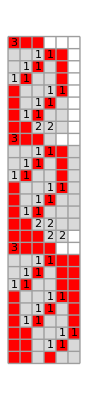
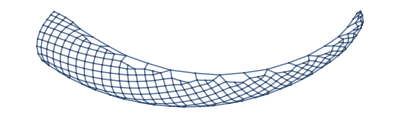
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss01a=SSS[rs01,"BBB",800, SSSMax->27,NetMax->384-82,HighlightMethod->Number,RulePlacement->Bottom,ImageSize->62.,NetSize->{Automatic,189.},SSSSize->{Automatic,250},VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->False];
```

```mathematica
nds01a=ToNetDifferenceSets[sss01a[["Net"]]]; nds01a//Short
```

{{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},«781»,{3},{1,3},{1,3},{3},{1,3},{1,3},{3},{1},{1}}

```mathematica
ReduceSetList[nds01a]  (* This will still fail, there's a bug to find! *)
```

{{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,44},€^13[€^2[{1,3}],{3,42}],{1,51},{1,2},{1,42},{44},{1,2,3},€^2[{1,3}],{3,45},€^5[€^2[{1,3}],{3,43}],€^8[€^2[{1,3}],{3}],€_(n$1⊨1)^2[{1,4-2 (-1+n$1)}],{1},€^2[{}],{1,2,3},€^4[€^2[{1,3}],{3}],€^2[{1}]}

Rather than constructing the IC again by hand, let’s take our previous summary, rsl01IC, but roll it back:

```mathematica
rsl01IC
```

{€_(k⊨1)^13[€_(j⊨1)^2[{2 (-1+j)+3 k}],{1,2,3},€^2[{1,3}],{3,2+3 k},€^(-1+k)[€^2[{1,3}],{3,3 k}],{1,9+3 k},{1,2},{1,3 k},{2+3 k},{1,2,3},€^2[{1,3}],{3,3+3 k},€^(-1+k)[€^2[{1,3}],{3,1+3 k}],{1,4},{1,2},{1,1+3 k}]}

```mathematica
rsl01aIC=RollBackIC@rsl01IC
```

{€_(k⊨1)^13[{1,2,3},€^2[{1,3}],{3,2+3 k},€^(-1+k)[€^2[{1,3}],{3,3 k}],{1,9+3 k},{1,2},{1,3 k},{2+3 k},{1,2,3},€^2[{1,3}],{3,3+3 k},€^(-1+k)[€^2[{1,3}],{3,1+3 k}],{1,4},{1,2},{1,1+3 k},€_(j⊨1)^2[{1+2 j+3 k}]]}

```mathematica
SequencePosition[nds01a,rsl01aIC//ExpandAll]
```

{{1,689}}

```mathematica
Equal@@{nds01a[[1;;689]],ExpandAll@rsl01aIC}
```

True

I love it when a plan comes together!

```mathematica
Transpose@{nds01a[[1;;689]],(ExpandAll@rsl01aIC)}//Grid
```

{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,5} | {3,5}
{1,12} | {1,12}
{1,2} | {1,2}
{1,3} | {1,3}
{5} | {5}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,6} | {3,6}
{1,4} | {1,4}
{1,2} | {1,2}
{1,4} | {1,4}
{6} | {6}
{8} | {8}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,8} | {3,8}
{1,3} | {1,3}
{1,3} | {1,3}
{3,6} | {3,6}
{1,15} | {1,15}
{1,2} | {1,2}
{1,6} | {1,6}
{8} | {8}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,3} | {1,3}
{1,3} | {1,3}
{3,7} | {3,7}
{1,4} | {1,4}
{1,2} | {1,2}
{1,7} | {1,7}
{9} | {9}
{11} | {11}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,11} | {3,11}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,3} | {1,3}
{1,3} | {1,3}
{3,9} | {3,9}
{1,18} | {1,18}
{1,2} | {1,2}
{1,9} | {1,9}
{11} | {11}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,10} | {3,10}
{1,3} | {1,3}
{1,3} | {1,3}
{3,10} | {3,10}
{1,4} | {1,4}
{1,2} | {1,2}
{1,10} | {1,10}
{12} | {12}
{14} | {14}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,14} | {3,14}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,3} | {1,3}
{1,3} | {1,3}
{3,12} | {3,12}
{1,21} | {1,21}
{1,2} | {1,2}
{1,12} | {1,12}
{14} | {14}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,3} | {1,3}
{1,3} | {1,3}
{3,13} | {3,13}
{1,4} | {1,4}
{1,2} | {1,2}
{1,13} | {1,13}
{15} | {15}
{17} | {17}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,17} | {3,17}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,3} | {1,3}
{1,3} | {1,3}
{3,15} | {3,15}
{1,24} | {1,24}
{1,2} | {1,2}
{1,15} | {1,15}
{17} | {17}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,3} | {1,3}
{1,3} | {1,3}
{3,16} | {3,16}
{1,4} | {1,4}
{1,2} | {1,2}
{1,16} | {1,16}
{18} | {18}
{20} | {20}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,20} | {3,20}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,3} | {1,3}
{1,3} | {1,3}
{3,18} | {3,18}
{1,27} | {1,27}
{1,2} | {1,2}
{1,18} | {1,18}
{20} | {20}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,3} | {1,3}
{1,3} | {1,3}
{3,19} | {3,19}
{1,4} | {1,4}
{1,2} | {1,2}
{1,19} | {1,19}
{21} | {21}
{23} | {23}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,23} | {3,23}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,3} | {1,3}
{1,3} | {1,3}
{3,21} | {3,21}
{1,30} | {1,30}
{1,2} | {1,2}
{1,21} | {1,21}
{23} | {23}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,3} | {1,3}
{1,3} | {1,3}
{3,22} | {3,22}
{1,4} | {1,4}
{1,2} | {1,2}
{1,22} | {1,22}
{24} | {24}
{26} | {26}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,26} | {3,26}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,3} | {1,3}
{1,3} | {1,3}
{3,24} | {3,24}
{1,33} | {1,33}
{1,2} | {1,2}
{1,24} | {1,24}
{26} | {26}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,3} | {1,3}
{1,3} | {1,3}
{3,25} | {3,25}
{1,4} | {1,4}
{1,2} | {1,2}
{1,25} | {1,25}
{27} | {27}
{29} | {29}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,29} | {3,29}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,3} | {1,3}
{1,3} | {1,3}
{3,27} | {3,27}
{1,36} | {1,36}
{1,2} | {1,2}
{1,27} | {1,27}
{29} | {29}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,3} | {1,3}
{1,3} | {1,3}
{3,28} | {3,28}
{1,4} | {1,4}
{1,2} | {1,2}
{1,28} | {1,28}
{30} | {30}
{32} | {32}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,32} | {3,32}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,3} | {1,3}
{1,3} | {1,3}
{3,30} | {3,30}
{1,39} | {1,39}
{1,2} | {1,2}
{1,30} | {1,30}
{32} | {32}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,3} | {1,3}
{1,3} | {1,3}
{3,31} | {3,31}
{1,4} | {1,4}
{1,2} | {1,2}
{1,31} | {1,31}
{33} | {33}
{35} | {35}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,35} | {3,35}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,3} | {1,3}
{1,3} | {1,3}
{3,33} | {3,33}
{1,42} | {1,42}
{1,2} | {1,2}
{1,33} | {1,33}
{35} | {35}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,3} | {1,3}
{1,3} | {1,3}
{3,34} | {3,34}
{1,4} | {1,4}
{1,2} | {1,2}
{1,34} | {1,34}
{36} | {36}
{38} | {38}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,38} | {3,38}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,3} | {1,3}
{1,3} | {1,3}
{3,36} | {3,36}
{1,45} | {1,45}
{1,2} | {1,2}
{1,36} | {1,36}
{38} | {38}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,3} | {1,3}
{1,3} | {1,3}
{3,37} | {3,37}
{1,4} | {1,4}
{1,2} | {1,2}
{1,37} | {1,37}
{39} | {39}
{41} | {41}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,41} | {3,41}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,3} | {1,3}
{1,3} | {1,3}
{3,39} | {3,39}
{1,48} | {1,48}
{1,2} | {1,2}
{1,39} | {1,39}
{41} | {41}
{1,2,3} | {1,2,3}
{1,3} | {1,3}
{1,3} | {1,3}
{3,42} | {3,42}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,3} | {1,3}
{1,3} | {1,3}
{3,40} | {3,40}
{1,4} | {1,4}
{1,2} | {1,2}
{1,40} | {1,40}
{42} | {42}
{44} | {44}

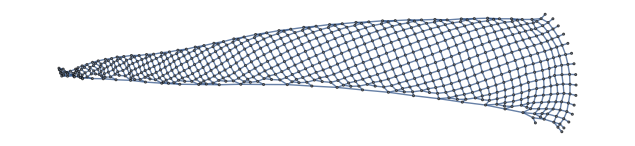

```mathematica
GraphPlot[FromNetDifferenceSets@ExpandAll@rsl01aIC]
```

### Bottom Line:

RuleSet & IC form:

```mathematica
<|"Index"->6308190100,"QCode"->"34243232424233","RuleSet"->{"AB"->"BA","AA"->"B","B"->"AAA"}|>
```

Best initial state string:

```mathematica
"BBB"
```

```mathematica
rsl01aIC
```

```mathematica
{€_(k⊨1)^13[{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,3 k+9},{1,2},{1,3 k},{2+3 k},
     {1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1},€_(j⊨1)^2[{1+2 j+3 k}]]}
```

### Below the Bottom Line:

Note: The items in cyan are the same, the ones in pink offer the possibility for further reduction with an index i=1 to 2, but the items in yellow don’t correspond to a simple pattern.  Still, I think I could do it by hand:

```mathematica
{€_(k⊨1)^13[{1,2,3},€^2[{1,3}],{3,3 k+2},€^(k-1)[€^2[{1,3}],{3,3 k}],{1,4+3 k+5},{1,2},{1,3 k},€_(j⊨1)^1[{2+3 k}],
     {1,2,3},€^2[{1,3}],{3,3 k+3},€^(k-1)[€^2[{1,3}],{3,3 k+1}],{1,4},{1,2},{1,3 k+1},€_(j⊨1)^2[{1+2 j+3 k}]]
```

```mathematica
{€_(k⊨1)^13[
€_(i⊨0)^1[{1,2,3},€^2[{1,3}],{3,3 k+i+2},€^(k-1)[€^2[{1,3}],{3,3 k+i}],{1,4+(1-i)*(3 k+5)},{1,2},{1,3 k+i},€_(j⊨1)^(i+1)[{i+2+3 k}]
]
]
```

```mathematica
{IndexedConcatenate[IndexedConcatenate[{1,2,3},IndexedConcatenate[{1,3},2],{3,2+3k+i},IndexedConcatenate[IndexedConcatenate[{1,3},2],{3,3k+i},k-1],{1,4+(1-i)(3*k+5)},{1,2},{1,3k+i},IndexedConcatenate[{i+2j+3k},{j,1,i+1}],{i,0,1}],{k,1,13}]}
```

{€_(k⊨1)^13[€_(i⊨0)^1[{1,2,3},€^2[{1,3}],{3,i+3 k+2},€^(k-1)[€^2[{1,3}],{3,i+3 k}],{1,(1-i) (3 k+5)+4},{1,2},{1,i+3 k},€_(j⊨1)^(i+1)[{i+2 j+3 k}]]]}

```mathematica
ExpandAll[%254] ==ExpandAll[rsl01aIC]
```

True

### Why did ReduceSetList fail here?

Reminder: make window half-width now

```mathematica
$debug=True;
ReduceSetList[ExpandAll[rsl01aIC]]
$debug=False;
```

Entering ReduceSetList with: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

exact repLen = 1: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[{1,3}],{3,9},€^2[{1,3}],{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[{1,3}],{3,10},€^2[{1,3}],{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},{1,4},{1,2},{1,40},{42},{44}}

Entering improveReduction with: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[{1,3}],{3,9},€^2[{1,3}],{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[{1,3}],{3,10},€^2[{1,3}],{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},{1,4},{1,2},{1,40},{42},{44}}

improved? : {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[{1,3}],{3,9},€^2[{1,3}],{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[{1,3}],{3,10},€^2[{1,3}],{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},{1,4},{1,2},{1,40},{42},{44}}

Entering ReduceSetList with: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[{1,3}],{3,9},€^2[{1,3}],{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[{1,3}],{3,10},€^2[{1,3}],{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},€^2[{1,3}],{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},€^2[{1,3}],{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},€^2[{1,3}],{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},€^2[{1,3}],{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},€^2[{1,3}],{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},€^2[{1,3}],{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},€^2[{1,3}],{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},€^2[{1,3}],{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},€^2[{1,3}],{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},€^2[{1,3}],{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},€^2[{1,3}],{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},€^2[{1,3}],{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},€^2[{1,3}],{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},€^2[{1,3}],{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},€^2[{1,3}],{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},€^2[{1,3}],{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},€^2[{1,3}],{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},€^2[{1,3}],{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},€^2[{1,3}],{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},€^2[{1,3}],{3,40},{1,4},{1,2},{1,40},{42},{44}}

exact repLen: 1

exact repLen: 2

Changed (in While): exact repLen = 2: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},{42},{44}}

Entering improveReduction with: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},{42},{44}}

improved? : {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},{42},{44}}

Entering ReduceSetList with: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},{42},{44}}

exact repLen: 1

exact repLen: 2

exact repLen: 3

exact repLen: 4

exact repLen: 5

exact repLen: 6

exact repLen: 7

exact repLen: 8

exact repLen: 9

exact repLen: 10

exact repLen: 11

exact repLen: 12

exact repLen: 13

exact repLen: 14

exact repLen: 15

exact repLen: 16

exact repLen: 17

exact repLen: 18

exact repLen: 19

exact repLen: 20

exact repLen: 21

exact repLen: 22

exact repLen: 23

exact repLen: 24

exact repLen: 25

exact repLen: 26

exact repLen: 27

exact repLen: 28

exact repLen: 29

exact repLen: 30

exact repLen: 31

exact repLen: 32

exact repLen: 33

exact repLen: 34

exact repLen: 35

exact repLen: 36

exact repLen: 37

exact repLen: 38

exact repLen: 39

exact repLen: 40

exact repLen: 41

exact repLen: 42

exact repLen: 43

exact repLen: 44

exact repLen: 45

exact repLen: 46

exact repLen: 47

exact repLen: 48

exact repLen: 49

exact repLen: 50

exact repLen: 51

exact repLen: 52

exact repLen: 53

exact repLen: 54

exact repLen: 55

exact repLen: 56

exact repLen: 57

exact repLen: 58

exact repLen: 59

exact repLen: 60

exact repLen: 61

exact repLen: 62

exact repLen: 63

exact repLen: 64

exact repLen: 65

exact repLen: 66

exact repLen: 67

exact repLen: 68

exact repLen: 69

exact repLen: 70

exact repLen: 71

exact repLen: 72

exact repLen: 73

exact repLen: 74

exact repLen: 75

exact repLen: 76

exact repLen: 77

exact repLen: 78

exact repLen: 79

exact repLen: 80

exact repLen: 81

exact repLen: 82

exact repLen: 83

exact repLen: 84

exact repLen: 85

exact repLen: 86

exact repLen: 87

exact repLen: 88

exact repLen: 89

exact repLen: 90

exact repLen: 91

exact repLen: 92

exact repLen: 93

exact repLen: 94

exact repLen: 95

exact repLen: 96

exact repLen: 97

exact repLen: 98

exact repLen: 99

exact repLen: 100

exact repLen: 101

exact repLen: 102

exact repLen: 103

exact repLen: 104

exact repLen: 105

exact repLen: 106

exact repLen: 107

exact repLen: 108

exact repLen: 109

exact repLen: 110

Exiting While[...replen...]

Treating Generic patterns

orig: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},{12},{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},{15},{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},{18},{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},{21},{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},{24},{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},{27},{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},{30},{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},{33},{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},{36},{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},{39},{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},{42},{44}}

generic: {{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{0}}

generic repLen: 1, pos: {{4,6},{11,13},{14,15},{21,23},{30,32},{33,34},{39,41},{47,49},{50,51},{56,58},{64,66},{67,68},{73,75},{81,83},{84,85},{90,92},{98,100},{101,102},{107,109},{115,117},{118,119},{124,126},{132,134},{135,136},{141,143},{149,151},{152,153},{158,160},{166,168},{169,170},{175,177},{183,185},{186,187},{192,194},{200,202},{203,204},{209,211},{217,219},{220,221}}

new varName: n$1

Entering FindSeqFns with:
 parted: {{{1,12}},{{1,2}},{{1,3}}}
 firstRep: {{1,12}}

Numerical Table to fit:
1 | 12
1 | 2
1 | 3

Function list: {1,FindSequenceFunction[{12,2,3},n$1]}

{{{1,12}},{{1,2}},{{1,3}}} : {{1,12}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{12,2,3},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{12,2,3},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{12,2,3},1]},{1,FindSequenceFunction[{12,2,3},2]},{1,FindSequenceFunction[{12,2,3},3]}}

ExpandAll[subseqList]: {{1,12},{1,2},{1,3}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,4}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 4

Function list: {1,FindSequenceFunction[{4,2,4},n$1]}

{{{1,4}},{{1,2}},{{1,4}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,4},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,4},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,4},1]},{1,FindSequenceFunction[{4,2,4},2]},{1,FindSequenceFunction[{4,2,4},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,4}}

(different)

Entering FindSeqFns with:
 parted: {{{6}},{{8}}}
 firstRep: {{6}}

Numerical Table to fit:
6
8

Function list: {6+2 (-1+n$1)}

{{{6}},{{8}}} : {{6}}

{{1,1}}

{{6+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{6+2 (-1+n$1)}]}

ExpandAll[ans]: {{6},{8}}

ExpandAll[subseqList]: {{6},{8}}

(same)

Entering FindSeqFns with:
 parted: {{{1,15}},{{1,2}},{{1,6}}}
 firstRep: {{1,15}}

Numerical Table to fit:
1 | 15
1 | 2
1 | 6

Function list: {1,FindSequenceFunction[{15,2,6},n$1]}

{{{1,15}},{{1,2}},{{1,6}}} : {{1,15}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{15,2,6},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{15,2,6},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{15,2,6},1]},{1,FindSequenceFunction[{15,2,6},2]},{1,FindSequenceFunction[{15,2,6},3]}}

ExpandAll[subseqList]: {{1,15},{1,2},{1,6}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,7}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 7

Function list: {1,FindSequenceFunction[{4,2,7},n$1]}

{{{1,4}},{{1,2}},{{1,7}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,7},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,7},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,7},1]},{1,FindSequenceFunction[{4,2,7},2]},{1,FindSequenceFunction[{4,2,7},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,7}}

(different)

Entering FindSeqFns with:
 parted: {{{9}},{{11}}}
 firstRep: {{9}}

Numerical Table to fit:
9
11

Function list: {9+2 (-1+n$1)}

{{{9}},{{11}}} : {{9}}

{{1,1}}

{{9+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{9+2 (-1+n$1)}]}

ExpandAll[ans]: {{9},{11}}

ExpandAll[subseqList]: {{9},{11}}

(same)

Entering FindSeqFns with:
 parted: {{{1,18}},{{1,2}},{{1,9}}}
 firstRep: {{1,18}}

Numerical Table to fit:
1 | 18
1 | 2
1 | 9

Function list: {1,FindSequenceFunction[{18,2,9},n$1]}

{{{1,18}},{{1,2}},{{1,9}}} : {{1,18}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{18,2,9},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{18,2,9},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{18,2,9},1]},{1,FindSequenceFunction[{18,2,9},2]},{1,FindSequenceFunction[{18,2,9},3]}}

ExpandAll[subseqList]: {{1,18},{1,2},{1,9}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,10}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 10

Function list: {1,FindSequenceFunction[{4,2,10},n$1]}

{{{1,4}},{{1,2}},{{1,10}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,10},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,10},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,10},1]},{1,FindSequenceFunction[{4,2,10},2]},{1,FindSequenceFunction[{4,2,10},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,10}}

(different)

Entering FindSeqFns with:
 parted: {{{12}},{{14}}}
 firstRep: {{12}}

Numerical Table to fit:
12
14

Function list: {12+2 (-1+n$1)}

{{{12}},{{14}}} : {{12}}

{{1,1}}

{{12+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{12+2 (-1+n$1)}]}

ExpandAll[ans]: {{12},{14}}

ExpandAll[subseqList]: {{12},{14}}

(same)

Entering FindSeqFns with:
 parted: {{{1,21}},{{1,2}},{{1,12}}}
 firstRep: {{1,21}}

Numerical Table to fit:
1 | 21
1 | 2
1 | 12

Function list: {1,FindSequenceFunction[{21,2,12},n$1]}

{{{1,21}},{{1,2}},{{1,12}}} : {{1,21}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{21,2,12},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{21,2,12},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{21,2,12},1]},{1,FindSequenceFunction[{21,2,12},2]},{1,FindSequenceFunction[{21,2,12},3]}}

ExpandAll[subseqList]: {{1,21},{1,2},{1,12}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,13}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 13

Function list: {1,FindSequenceFunction[{4,2,13},n$1]}

{{{1,4}},{{1,2}},{{1,13}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,13},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,13},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,13},1]},{1,FindSequenceFunction[{4,2,13},2]},{1,FindSequenceFunction[{4,2,13},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,13}}

(different)

Entering FindSeqFns with:
 parted: {{{15}},{{17}}}
 firstRep: {{15}}

Numerical Table to fit:
15
17

Function list: {15+2 (-1+n$1)}

{{{15}},{{17}}} : {{15}}

{{1,1}}

{{15+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{15+2 (-1+n$1)}]}

ExpandAll[ans]: {{15},{17}}

ExpandAll[subseqList]: {{15},{17}}

(same)

Entering FindSeqFns with:
 parted: {{{1,24}},{{1,2}},{{1,15}}}
 firstRep: {{1,24}}

Numerical Table to fit:
1 | 24
1 | 2
1 | 15

Function list: {1,FindSequenceFunction[{24,2,15},n$1]}

{{{1,24}},{{1,2}},{{1,15}}} : {{1,24}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{24,2,15},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{24,2,15},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{24,2,15},1]},{1,FindSequenceFunction[{24,2,15},2]},{1,FindSequenceFunction[{24,2,15},3]}}

ExpandAll[subseqList]: {{1,24},{1,2},{1,15}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,16}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 16

Function list: {1,FindSequenceFunction[{4,2,16},n$1]}

{{{1,4}},{{1,2}},{{1,16}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,16},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,16},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,16},1]},{1,FindSequenceFunction[{4,2,16},2]},{1,FindSequenceFunction[{4,2,16},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,16}}

(different)

Entering FindSeqFns with:
 parted: {{{18}},{{20}}}
 firstRep: {{18}}

Numerical Table to fit:
18
20

Function list: {18+2 (-1+n$1)}

{{{18}},{{20}}} : {{18}}

{{1,1}}

{{18+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{18+2 (-1+n$1)}]}

ExpandAll[ans]: {{18},{20}}

ExpandAll[subseqList]: {{18},{20}}

(same)

Entering FindSeqFns with:
 parted: {{{1,27}},{{1,2}},{{1,18}}}
 firstRep: {{1,27}}

Numerical Table to fit:
1 | 27
1 | 2
1 | 18

Function list: {1,FindSequenceFunction[{27,2,18},n$1]}

{{{1,27}},{{1,2}},{{1,18}}} : {{1,27}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{27,2,18},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{27,2,18},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{27,2,18},1]},{1,FindSequenceFunction[{27,2,18},2]},{1,FindSequenceFunction[{27,2,18},3]}}

ExpandAll[subseqList]: {{1,27},{1,2},{1,18}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,19}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 19

Function list: {1,FindSequenceFunction[{4,2,19},n$1]}

{{{1,4}},{{1,2}},{{1,19}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,19},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,19},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,19},1]},{1,FindSequenceFunction[{4,2,19},2]},{1,FindSequenceFunction[{4,2,19},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,19}}

(different)

Entering FindSeqFns with:
 parted: {{{21}},{{23}}}
 firstRep: {{21}}

Numerical Table to fit:
21
23

Function list: {21+2 (-1+n$1)}

{{{21}},{{23}}} : {{21}}

{{1,1}}

{{21+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{21+2 (-1+n$1)}]}

ExpandAll[ans]: {{21},{23}}

ExpandAll[subseqList]: {{21},{23}}

(same)

Entering FindSeqFns with:
 parted: {{{1,30}},{{1,2}},{{1,21}}}
 firstRep: {{1,30}}

Numerical Table to fit:
1 | 30
1 | 2
1 | 21

Function list: {1,FindSequenceFunction[{30,2,21},n$1]}

{{{1,30}},{{1,2}},{{1,21}}} : {{1,30}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{30,2,21},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{30,2,21},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{30,2,21},1]},{1,FindSequenceFunction[{30,2,21},2]},{1,FindSequenceFunction[{30,2,21},3]}}

ExpandAll[subseqList]: {{1,30},{1,2},{1,21}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,22}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 22

Function list: {1,FindSequenceFunction[{4,2,22},n$1]}

{{{1,4}},{{1,2}},{{1,22}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,22},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,22},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,22},1]},{1,FindSequenceFunction[{4,2,22},2]},{1,FindSequenceFunction[{4,2,22},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,22}}

(different)

Entering FindSeqFns with:
 parted: {{{24}},{{26}}}
 firstRep: {{24}}

Numerical Table to fit:
24
26

Function list: {24+2 (-1+n$1)}

{{{24}},{{26}}} : {{24}}

{{1,1}}

{{24+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{24+2 (-1+n$1)}]}

ExpandAll[ans]: {{24},{26}}

ExpandAll[subseqList]: {{24},{26}}

(same)

Entering FindSeqFns with:
 parted: {{{1,33}},{{1,2}},{{1,24}}}
 firstRep: {{1,33}}

Numerical Table to fit:
1 | 33
1 | 2
1 | 24

Function list: {1,FindSequenceFunction[{33,2,24},n$1]}

{{{1,33}},{{1,2}},{{1,24}}} : {{1,33}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{33,2,24},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{33,2,24},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{33,2,24},1]},{1,FindSequenceFunction[{33,2,24},2]},{1,FindSequenceFunction[{33,2,24},3]}}

ExpandAll[subseqList]: {{1,33},{1,2},{1,24}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,25}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 25

Function list: {1,FindSequenceFunction[{4,2,25},n$1]}

{{{1,4}},{{1,2}},{{1,25}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,25},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,25},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,25},1]},{1,FindSequenceFunction[{4,2,25},2]},{1,FindSequenceFunction[{4,2,25},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,25}}

(different)

Entering FindSeqFns with:
 parted: {{{27}},{{29}}}
 firstRep: {{27}}

Numerical Table to fit:
27
29

Function list: {27+2 (-1+n$1)}

{{{27}},{{29}}} : {{27}}

{{1,1}}

{{27+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{27+2 (-1+n$1)}]}

ExpandAll[ans]: {{27},{29}}

ExpandAll[subseqList]: {{27},{29}}

(same)

Entering FindSeqFns with:
 parted: {{{1,36}},{{1,2}},{{1,27}}}
 firstRep: {{1,36}}

Numerical Table to fit:
1 | 36
1 | 2
1 | 27

Function list: {1,FindSequenceFunction[{36,2,27},n$1]}

{{{1,36}},{{1,2}},{{1,27}}} : {{1,36}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{36,2,27},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{36,2,27},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{36,2,27},1]},{1,FindSequenceFunction[{36,2,27},2]},{1,FindSequenceFunction[{36,2,27},3]}}

ExpandAll[subseqList]: {{1,36},{1,2},{1,27}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,28}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 28

Function list: {1,FindSequenceFunction[{4,2,28},n$1]}

{{{1,4}},{{1,2}},{{1,28}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,28},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,28},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,28},1]},{1,FindSequenceFunction[{4,2,28},2]},{1,FindSequenceFunction[{4,2,28},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,28}}

(different)

Entering FindSeqFns with:
 parted: {{{30}},{{32}}}
 firstRep: {{30}}

Numerical Table to fit:
30
32

Function list: {30+2 (-1+n$1)}

{{{30}},{{32}}} : {{30}}

{{1,1}}

{{30+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{30+2 (-1+n$1)}]}

ExpandAll[ans]: {{30},{32}}

ExpandAll[subseqList]: {{30},{32}}

(same)

Entering FindSeqFns with:
 parted: {{{1,39}},{{1,2}},{{1,30}}}
 firstRep: {{1,39}}

Numerical Table to fit:
1 | 39
1 | 2
1 | 30

Function list: {1,FindSequenceFunction[{39,2,30},n$1]}

{{{1,39}},{{1,2}},{{1,30}}} : {{1,39}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{39,2,30},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{39,2,30},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{39,2,30},1]},{1,FindSequenceFunction[{39,2,30},2]},{1,FindSequenceFunction[{39,2,30},3]}}

ExpandAll[subseqList]: {{1,39},{1,2},{1,30}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,31}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 31

Function list: {1,FindSequenceFunction[{4,2,31},n$1]}

{{{1,4}},{{1,2}},{{1,31}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,31},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,31},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,31},1]},{1,FindSequenceFunction[{4,2,31},2]},{1,FindSequenceFunction[{4,2,31},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,31}}

(different)

Entering FindSeqFns with:
 parted: {{{33}},{{35}}}
 firstRep: {{33}}

Numerical Table to fit:
33
35

Function list: {33+2 (-1+n$1)}

{{{33}},{{35}}} : {{33}}

{{1,1}}

{{33+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{33+2 (-1+n$1)}]}

ExpandAll[ans]: {{33},{35}}

ExpandAll[subseqList]: {{33},{35}}

(same)

Entering FindSeqFns with:
 parted: {{{1,42}},{{1,2}},{{1,33}}}
 firstRep: {{1,42}}

Numerical Table to fit:
1 | 42
1 | 2
1 | 33

Function list: {1,FindSequenceFunction[{42,2,33},n$1]}

{{{1,42}},{{1,2}},{{1,33}}} : {{1,42}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{42,2,33},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{42,2,33},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{42,2,33},1]},{1,FindSequenceFunction[{42,2,33},2]},{1,FindSequenceFunction[{42,2,33},3]}}

ExpandAll[subseqList]: {{1,42},{1,2},{1,33}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,34}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 34

Function list: {1,FindSequenceFunction[{4,2,34},n$1]}

{{{1,4}},{{1,2}},{{1,34}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,34},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,34},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,34},1]},{1,FindSequenceFunction[{4,2,34},2]},{1,FindSequenceFunction[{4,2,34},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,34}}

(different)

Entering FindSeqFns with:
 parted: {{{36}},{{38}}}
 firstRep: {{36}}

Numerical Table to fit:
36
38

Function list: {36+2 (-1+n$1)}

{{{36}},{{38}}} : {{36}}

{{1,1}}

{{36+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{36+2 (-1+n$1)}]}

ExpandAll[ans]: {{36},{38}}

ExpandAll[subseqList]: {{36},{38}}

(same)

Entering FindSeqFns with:
 parted: {{{1,45}},{{1,2}},{{1,36}}}
 firstRep: {{1,45}}

Numerical Table to fit:
1 | 45
1 | 2
1 | 36

Function list: {1,FindSequenceFunction[{45,2,36},n$1]}

{{{1,45}},{{1,2}},{{1,36}}} : {{1,45}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{45,2,36},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{45,2,36},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{45,2,36},1]},{1,FindSequenceFunction[{45,2,36},2]},{1,FindSequenceFunction[{45,2,36},3]}}

ExpandAll[subseqList]: {{1,45},{1,2},{1,36}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,37}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 37

Function list: {1,FindSequenceFunction[{4,2,37},n$1]}

{{{1,4}},{{1,2}},{{1,37}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,37},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,37},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,37},1]},{1,FindSequenceFunction[{4,2,37},2]},{1,FindSequenceFunction[{4,2,37},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,37}}

(different)

Entering FindSeqFns with:
 parted: {{{39}},{{41}}}
 firstRep: {{39}}

Numerical Table to fit:
39
41

Function list: {39+2 (-1+n$1)}

{{{39}},{{41}}} : {{39}}

{{1,1}}

{{39+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{39+2 (-1+n$1)}]}

ExpandAll[ans]: {{39},{41}}

ExpandAll[subseqList]: {{39},{41}}

(same)

Entering FindSeqFns with:
 parted: {{{1,48}},{{1,2}},{{1,39}}}
 firstRep: {{1,48}}

Numerical Table to fit:
1 | 48
1 | 2
1 | 39

Function list: {1,FindSequenceFunction[{48,2,39},n$1]}

{{{1,48}},{{1,2}},{{1,39}}} : {{1,48}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{48,2,39},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{48,2,39},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{48,2,39},1]},{1,FindSequenceFunction[{48,2,39},2]},{1,FindSequenceFunction[{48,2,39},3]}}

ExpandAll[subseqList]: {{1,48},{1,2},{1,39}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,40}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 40

Function list: {1,FindSequenceFunction[{4,2,40},n$1]}

{{{1,4}},{{1,2}},{{1,40}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,40},n$1]}}

ans: {€_(n$1⊨1)^3[{1,FindSequenceFunction[{4,2,40},n$1]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,40},1]},{1,FindSequenceFunction[{4,2,40},2]},{1,FindSequenceFunction[{4,2,40},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,40}}

(different)

Entering FindSeqFns with:
 parted: {{{42}},{{44}}}
 firstRep: {{42}}

Numerical Table to fit:
42
44

Function list: {42+2 (-1+n$1)}

{{{42}},{{44}}} : {{42}}

{{1,1}}

{{42+2 (-1+n$1)}}

ans: {€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[ans]: {{42},{44}}

ExpandAll[subseqList]: {{42},{44}}

(same)

generic repLen = 1: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Entering improveReduction with: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 14 (of {14,32,48,64,80,96,112,128,144,160,176,192,208})
Length[p] = 13, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{6+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (1+n$1)}}

leftEltsToDrop: {{4}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{4}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (1+n$1)}]
rightLNew: {{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (1+n$1)}]
rightLNew: {{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},€_(n$1⊨1)^2[{2 (1+n$1)}],{8},{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{6+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{6+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 32 (of {32,48,64,80,96,112,128,144,160,176,192,208})
Length[p] = 12, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{9+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{5+2 n$1}}

leftEltsToDrop: {{7}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{7}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{5+2 n$1}]
rightLNew: {{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{5+2 n$1}]
rightLNew: {{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},€_(n$1⊨1)^2[{5+2 n$1}],{11},{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{9+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{9+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 48 (of {48,64,80,96,112,128,144,160,176,192,208})
Length[p] = 11, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{12+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (4+n$1)}}

leftEltsToDrop: {{10}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{10}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (4+n$1)}]
rightLNew: {{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (4+n$1)}]
rightLNew: {{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (4+n$1)}],{14},{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{12+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{12+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 64 (of {64,80,96,112,128,144,160,176,192,208})
Length[p] = 10, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{15+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{11+2 n$1}}

leftEltsToDrop: {{13}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{13}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{11+2 n$1}]
rightLNew: {{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{11+2 n$1}]
rightLNew: {{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},€_(n$1⊨1)^2[{11+2 n$1}],{17},{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{15+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{15+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 80 (of {80,96,112,128,144,160,176,192,208})
Length[p] = 9, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{18+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (7+n$1)}}

leftEltsToDrop: {{16}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{16}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (7+n$1)}]
rightLNew: {{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (7+n$1)}]
rightLNew: {{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (7+n$1)}],{20},{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{18+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{18+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 96 (of {96,112,128,144,160,176,192,208})
Length[p] = 8, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{21+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{17+2 n$1}}

leftEltsToDrop: {{19}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{19}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{17+2 n$1}]
rightLNew: {{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{17+2 n$1}]
rightLNew: {{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},€_(n$1⊨1)^2[{17+2 n$1}],{23},{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{21+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{21+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 112 (of {112,128,144,160,176,192,208})
Length[p] = 7, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{24+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (10+n$1)}}

leftEltsToDrop: {{22}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{22}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (10+n$1)}]
rightLNew: {{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (10+n$1)}]
rightLNew: {{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (10+n$1)}],{26},{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{24+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{24+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 128 (of {128,144,160,176,192,208})
Length[p] = 6, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{27+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{23+2 n$1}}

leftEltsToDrop: {{25}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{25}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{23+2 n$1}]
rightLNew: {{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{23+2 n$1}]
rightLNew: {{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},€_(n$1⊨1)^2[{23+2 n$1}],{29},{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{27+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{27+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 144 (of {144,160,176,192,208})
Length[p] = 5, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{30+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (13+n$1)}}

leftEltsToDrop: {{28}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{28}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (13+n$1)}]
rightLNew: {{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (13+n$1)}]
rightLNew: {{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (13+n$1)}],{32},{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{30+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{30+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 160 (of {160,176,192,208})
Length[p] = 4, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{33+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{29+2 n$1}}

leftEltsToDrop: {{31}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{31}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{29+2 n$1}]
rightLNew: {{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{29+2 n$1}]
rightLNew: {{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},€_(n$1⊨1)^2[{29+2 n$1}],{35},{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{33+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{33+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 176 (of {176,192,208})
Length[p] = 3, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{36+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (16+n$1)}}

leftEltsToDrop: {{34}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{34}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (16+n$1)}]
rightLNew: {{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (16+n$1)}]
rightLNew: {{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (16+n$1)}],{38},{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{36+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{36+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 192 (of {192,208})
Length[p] = 2, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{39+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{35+2 n$1}}

leftEltsToDrop: {{37}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{37}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{35+2 n$1}]
rightLNew: {{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{35+2 n$1}]
rightLNew: {{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},€_(n$1⊨1)^2[{35+2 n$1}],{41},{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{39+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

rightLNew: {{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

midElNew: €_(n$1⊨1)^2[{39+2 (-1+n$1)}]

rightLNew: {{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

Trying to improve reduction at pos: 208 (of {208})
Length[p] = 1, Length[l0] = 208

Before roll attempt: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

oldArgList: {{42+2 (-1+n$1)}}

iter: {n$1,1,2} : 
 iterVar = n$1
 iterStart = 1
 iterStop = 2

newArgList: {{2 (19+n$1)}}

leftEltsToDrop: {{40}}

old value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40}}

new value of leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2}}

dropping last 1 element(s) from leftEltsToDrop: {{40}}

new leftEltsToDrop: {}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (19+n$1)}]
rightLNew: {{44}}

countRolled: 1

roll gives different result:

wholeL: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{1,40},{42},{44}}

leftLNew: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2}}
MidElNew: €_(n$1⊨1)^2[{2 (19+n$1)}]
rightLNew: {{44}}

new stuff: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},€_(n$1⊨1)^2[{2 (19+n$1)}],{44}}

ExpandAll[new stuff]: {{1,2,3},{1,3},{1,3},{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},{1,3},{1,3},{3,6},{1,4},{1,2},{1,4},{6},{8},{1,2,3},{1,3},{1,3},{3,8},{1,3},{1,3},{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},{1,3},{1,3},{3,9},{1,3},{1,3},{3,7},{1,4},{1,2},{1,7},{9},{11},{1,2,3},{1,3},{1,3},{3,11},{1,3},{1,3},{3,9},{1,3},{1,3},{3,9},{1,18},{1,2},{1,9},{11},{1,2,3},{1,3},{1,3},{3,12},{1,3},{1,3},{3,10},{1,3},{1,3},{3,10},{1,4},{1,2},{1,10},{12},{14},{1,2,3},{1,3},{1,3},{3,14},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,3},{1,3},{3,12},{1,21},{1,2},{1,12},{14},{1,2,3},{1,3},{1,3},{3,15},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,3},{1,3},{3,13},{1,4},{1,2},{1,13},{15},{17},{1,2,3},{1,3},{1,3},{3,17},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,3},{1,3},{3,15},{1,24},{1,2},{1,15},{17},{1,2,3},{1,3},{1,3},{3,18},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,3},{1,3},{3,16},{1,4},{1,2},{1,16},{18},{20},{1,2,3},{1,3},{1,3},{3,20},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,3},{1,3},{3,18},{1,27},{1,2},{1,18},{20},{1,2,3},{1,3},{1,3},{3,21},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,3},{1,3},{3,19},{1,4},{1,2},{1,19},{21},{23},{1,2,3},{1,3},{1,3},{3,23},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,3},{1,3},{3,21},{1,30},{1,2},{1,21},{23},{1,2,3},{1,3},{1,3},{3,24},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,3},{1,3},{3,22},{1,4},{1,2},{1,22},{24},{26},{1,2,3},{1,3},{1,3},{3,26},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,3},{1,3},{3,24},{1,33},{1,2},{1,24},{26},{1,2,3},{1,3},{1,3},{3,27},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,3},{1,3},{3,25},{1,4},{1,2},{1,25},{27},{29},{1,2,3},{1,3},{1,3},{3,29},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,3},{1,3},{3,27},{1,36},{1,2},{1,27},{29},{1,2,3},{1,3},{1,3},{3,30},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,3},{1,3},{3,28},{1,4},{1,2},{1,28},{30},{32},{1,2,3},{1,3},{1,3},{3,32},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,3},{1,3},{3,30},{1,39},{1,2},{1,30},{32},{1,2,3},{1,3},{1,3},{3,33},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,3},{1,3},{3,31},{1,4},{1,2},{1,31},{33},{35},{1,2,3},{1,3},{1,3},{3,35},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,3},{1,3},{3,33},{1,42},{1,2},{1,33},{35},{1,2,3},{1,3},{1,3},{3,36},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,3},{1,3},{3,34},{1,4},{1,2},{1,34},{36},{38},{1,2,3},{1,3},{1,3},{3,38},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,3},{1,3},{3,36},{1,45},{1,2},{1,36},{38},{1,2,3},{1,3},{1,3},{3,39},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,3},{1,3},{3,37},{1,4},{1,2},{1,37},{39},{41},{1,2,3},{1,3},{1,3},{3,41},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,3},{1,3},{3,39},{1,48},{1,2},{1,39},{41},{1,2,3},{1,3},{1,3},{3,42},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,3},{1,3},{3,40},{1,4},{1,2},{40},{42},{44}}

Farthest left: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

countRolled: 0

midElNew: €_(n$1⊨1)^2[{42+2 (-1+n$1)}]

rightLNew: {}

countRolled: 0

rightLNew: {}

midElNew: €_(n$1⊨1)^2[{42+2 (-1+n$1)}]

rightLNew: {}

improved? : {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

orig: {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

generic: {{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}]}

generic repLen: 1, pos: {{4,6},{11,13},{20,22},{29,31},{37,39},{45,47},{53,55},{61,63},{69,71},{77,79},{85,87},{93,95},{101,103},{109,111},{117,119},{125,127},{133,135},{141,143},{149,151},{157,159},{165,167},{173,175},{181,183},{189,191},{197,199},{205,207}}

new varName: n$2

Entering FindSeqFns with:
 parted: {{{1,12}},{{1,2}},{{1,3}}}
 firstRep: {{1,12}}

Numerical Table to fit:
1 | 12
1 | 2
1 | 3

Function list: {1,FindSequenceFunction[{12,2,3},n$2]}

{{{1,12}},{{1,2}},{{1,3}}} : {{1,12}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{12,2,3},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{12,2,3},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{12,2,3},1]},{1,FindSequenceFunction[{12,2,3},2]},{1,FindSequenceFunction[{12,2,3},3]}}

ExpandAll[subseqList]: {{1,12},{1,2},{1,3}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,4}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 4

Function list: {1,FindSequenceFunction[{4,2,4},n$2]}

{{{1,4}},{{1,2}},{{1,4}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,4},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,4},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,4},1]},{1,FindSequenceFunction[{4,2,4},2]},{1,FindSequenceFunction[{4,2,4},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,4}}

(different)

Entering FindSeqFns with:
 parted: {{{1,15}},{{1,2}},{{1,6}}}
 firstRep: {{1,15}}

Numerical Table to fit:
1 | 15
1 | 2
1 | 6

Function list: {1,FindSequenceFunction[{15,2,6},n$2]}

{{{1,15}},{{1,2}},{{1,6}}} : {{1,15}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{15,2,6},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{15,2,6},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{15,2,6},1]},{1,FindSequenceFunction[{15,2,6},2]},{1,FindSequenceFunction[{15,2,6},3]}}

ExpandAll[subseqList]: {{1,15},{1,2},{1,6}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,7}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 7

Function list: {1,FindSequenceFunction[{4,2,7},n$2]}

{{{1,4}},{{1,2}},{{1,7}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,7},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,7},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,7},1]},{1,FindSequenceFunction[{4,2,7},2]},{1,FindSequenceFunction[{4,2,7},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,7}}

(different)

Entering FindSeqFns with:
 parted: {{{1,18}},{{1,2}},{{1,9}}}
 firstRep: {{1,18}}

Numerical Table to fit:
1 | 18
1 | 2
1 | 9

Function list: {1,FindSequenceFunction[{18,2,9},n$2]}

{{{1,18}},{{1,2}},{{1,9}}} : {{1,18}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{18,2,9},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{18,2,9},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{18,2,9},1]},{1,FindSequenceFunction[{18,2,9},2]},{1,FindSequenceFunction[{18,2,9},3]}}

ExpandAll[subseqList]: {{1,18},{1,2},{1,9}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,10}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 10

Function list: {1,FindSequenceFunction[{4,2,10},n$2]}

{{{1,4}},{{1,2}},{{1,10}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,10},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,10},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,10},1]},{1,FindSequenceFunction[{4,2,10},2]},{1,FindSequenceFunction[{4,2,10},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,10}}

(different)

Entering FindSeqFns with:
 parted: {{{1,21}},{{1,2}},{{1,12}}}
 firstRep: {{1,21}}

Numerical Table to fit:
1 | 21
1 | 2
1 | 12

Function list: {1,FindSequenceFunction[{21,2,12},n$2]}

{{{1,21}},{{1,2}},{{1,12}}} : {{1,21}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{21,2,12},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{21,2,12},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{21,2,12},1]},{1,FindSequenceFunction[{21,2,12},2]},{1,FindSequenceFunction[{21,2,12},3]}}

ExpandAll[subseqList]: {{1,21},{1,2},{1,12}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,13}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 13

Function list: {1,FindSequenceFunction[{4,2,13},n$2]}

{{{1,4}},{{1,2}},{{1,13}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,13},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,13},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,13},1]},{1,FindSequenceFunction[{4,2,13},2]},{1,FindSequenceFunction[{4,2,13},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,13}}

(different)

Entering FindSeqFns with:
 parted: {{{1,24}},{{1,2}},{{1,15}}}
 firstRep: {{1,24}}

Numerical Table to fit:
1 | 24
1 | 2
1 | 15

Function list: {1,FindSequenceFunction[{24,2,15},n$2]}

{{{1,24}},{{1,2}},{{1,15}}} : {{1,24}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{24,2,15},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{24,2,15},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{24,2,15},1]},{1,FindSequenceFunction[{24,2,15},2]},{1,FindSequenceFunction[{24,2,15},3]}}

ExpandAll[subseqList]: {{1,24},{1,2},{1,15}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,16}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 16

Function list: {1,FindSequenceFunction[{4,2,16},n$2]}

{{{1,4}},{{1,2}},{{1,16}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,16},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,16},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,16},1]},{1,FindSequenceFunction[{4,2,16},2]},{1,FindSequenceFunction[{4,2,16},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,16}}

(different)

Entering FindSeqFns with:
 parted: {{{1,27}},{{1,2}},{{1,18}}}
 firstRep: {{1,27}}

Numerical Table to fit:
1 | 27
1 | 2
1 | 18

Function list: {1,FindSequenceFunction[{27,2,18},n$2]}

{{{1,27}},{{1,2}},{{1,18}}} : {{1,27}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{27,2,18},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{27,2,18},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{27,2,18},1]},{1,FindSequenceFunction[{27,2,18},2]},{1,FindSequenceFunction[{27,2,18},3]}}

ExpandAll[subseqList]: {{1,27},{1,2},{1,18}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,19}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 19

Function list: {1,FindSequenceFunction[{4,2,19},n$2]}

{{{1,4}},{{1,2}},{{1,19}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,19},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,19},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,19},1]},{1,FindSequenceFunction[{4,2,19},2]},{1,FindSequenceFunction[{4,2,19},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,19}}

(different)

Entering FindSeqFns with:
 parted: {{{1,30}},{{1,2}},{{1,21}}}
 firstRep: {{1,30}}

Numerical Table to fit:
1 | 30
1 | 2
1 | 21

Function list: {1,FindSequenceFunction[{30,2,21},n$2]}

{{{1,30}},{{1,2}},{{1,21}}} : {{1,30}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{30,2,21},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{30,2,21},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{30,2,21},1]},{1,FindSequenceFunction[{30,2,21},2]},{1,FindSequenceFunction[{30,2,21},3]}}

ExpandAll[subseqList]: {{1,30},{1,2},{1,21}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,22}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 22

Function list: {1,FindSequenceFunction[{4,2,22},n$2]}

{{{1,4}},{{1,2}},{{1,22}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,22},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,22},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,22},1]},{1,FindSequenceFunction[{4,2,22},2]},{1,FindSequenceFunction[{4,2,22},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,22}}

(different)

Entering FindSeqFns with:
 parted: {{{1,33}},{{1,2}},{{1,24}}}
 firstRep: {{1,33}}

Numerical Table to fit:
1 | 33
1 | 2
1 | 24

Function list: {1,FindSequenceFunction[{33,2,24},n$2]}

{{{1,33}},{{1,2}},{{1,24}}} : {{1,33}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{33,2,24},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{33,2,24},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{33,2,24},1]},{1,FindSequenceFunction[{33,2,24},2]},{1,FindSequenceFunction[{33,2,24},3]}}

ExpandAll[subseqList]: {{1,33},{1,2},{1,24}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,25}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 25

Function list: {1,FindSequenceFunction[{4,2,25},n$2]}

{{{1,4}},{{1,2}},{{1,25}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,25},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,25},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,25},1]},{1,FindSequenceFunction[{4,2,25},2]},{1,FindSequenceFunction[{4,2,25},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,25}}

(different)

Entering FindSeqFns with:
 parted: {{{1,36}},{{1,2}},{{1,27}}}
 firstRep: {{1,36}}

Numerical Table to fit:
1 | 36
1 | 2
1 | 27

Function list: {1,FindSequenceFunction[{36,2,27},n$2]}

{{{1,36}},{{1,2}},{{1,27}}} : {{1,36}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{36,2,27},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{36,2,27},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{36,2,27},1]},{1,FindSequenceFunction[{36,2,27},2]},{1,FindSequenceFunction[{36,2,27},3]}}

ExpandAll[subseqList]: {{1,36},{1,2},{1,27}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,28}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 28

Function list: {1,FindSequenceFunction[{4,2,28},n$2]}

{{{1,4}},{{1,2}},{{1,28}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,28},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,28},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,28},1]},{1,FindSequenceFunction[{4,2,28},2]},{1,FindSequenceFunction[{4,2,28},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,28}}

(different)

Entering FindSeqFns with:
 parted: {{{1,39}},{{1,2}},{{1,30}}}
 firstRep: {{1,39}}

Numerical Table to fit:
1 | 39
1 | 2
1 | 30

Function list: {1,FindSequenceFunction[{39,2,30},n$2]}

{{{1,39}},{{1,2}},{{1,30}}} : {{1,39}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{39,2,30},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{39,2,30},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{39,2,30},1]},{1,FindSequenceFunction[{39,2,30},2]},{1,FindSequenceFunction[{39,2,30},3]}}

ExpandAll[subseqList]: {{1,39},{1,2},{1,30}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,31}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 31

Function list: {1,FindSequenceFunction[{4,2,31},n$2]}

{{{1,4}},{{1,2}},{{1,31}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,31},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,31},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,31},1]},{1,FindSequenceFunction[{4,2,31},2]},{1,FindSequenceFunction[{4,2,31},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,31}}

(different)

Entering FindSeqFns with:
 parted: {{{1,42}},{{1,2}},{{1,33}}}
 firstRep: {{1,42}}

Numerical Table to fit:
1 | 42
1 | 2
1 | 33

Function list: {1,FindSequenceFunction[{42,2,33},n$2]}

{{{1,42}},{{1,2}},{{1,33}}} : {{1,42}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{42,2,33},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{42,2,33},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{42,2,33},1]},{1,FindSequenceFunction[{42,2,33},2]},{1,FindSequenceFunction[{42,2,33},3]}}

ExpandAll[subseqList]: {{1,42},{1,2},{1,33}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,34}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 34

Function list: {1,FindSequenceFunction[{4,2,34},n$2]}

{{{1,4}},{{1,2}},{{1,34}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,34},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,34},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,34},1]},{1,FindSequenceFunction[{4,2,34},2]},{1,FindSequenceFunction[{4,2,34},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,34}}

(different)

Entering FindSeqFns with:
 parted: {{{1,45}},{{1,2}},{{1,36}}}
 firstRep: {{1,45}}

Numerical Table to fit:
1 | 45
1 | 2
1 | 36

Function list: {1,FindSequenceFunction[{45,2,36},n$2]}

{{{1,45}},{{1,2}},{{1,36}}} : {{1,45}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{45,2,36},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{45,2,36},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{45,2,36},1]},{1,FindSequenceFunction[{45,2,36},2]},{1,FindSequenceFunction[{45,2,36},3]}}

ExpandAll[subseqList]: {{1,45},{1,2},{1,36}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,37}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 37

Function list: {1,FindSequenceFunction[{4,2,37},n$2]}

{{{1,4}},{{1,2}},{{1,37}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,37},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,37},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,37},1]},{1,FindSequenceFunction[{4,2,37},2]},{1,FindSequenceFunction[{4,2,37},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,37}}

(different)

Entering FindSeqFns with:
 parted: {{{1,48}},{{1,2}},{{1,39}}}
 firstRep: {{1,48}}

Numerical Table to fit:
1 | 48
1 | 2
1 | 39

Function list: {1,FindSequenceFunction[{48,2,39},n$2]}

{{{1,48}},{{1,2}},{{1,39}}} : {{1,48}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{48,2,39},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{48,2,39},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{48,2,39},1]},{1,FindSequenceFunction[{48,2,39},2]},{1,FindSequenceFunction[{48,2,39},3]}}

ExpandAll[subseqList]: {{1,48},{1,2},{1,39}}

(different)

Entering FindSeqFns with:
 parted: {{{1,4}},{{1,2}},{{1,40}}}
 firstRep: {{1,4}}

Numerical Table to fit:
1 | 4
1 | 2
1 | 40

Function list: {1,FindSequenceFunction[{4,2,40},n$2]}

{{{1,4}},{{1,2}},{{1,40}}} : {{1,4}}

{{1,1},{1,2}}

{{1,FindSequenceFunction[{4,2,40},n$2]}}

ans: {€_(n$2⊨1)^3[{1,FindSequenceFunction[{4,2,40},n$2]}]}

ExpandAll[ans]: {{1,FindSequenceFunction[{4,2,40},1]},{1,FindSequenceFunction[{4,2,40},2]},{1,FindSequenceFunction[{4,2,40},3]}}

ExpandAll[subseqList]: {{1,4},{1,2},{1,40}}

(different)

reduced? : {{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

{{1,2,3},€^2[{1,3}],{3,5},{1,12},{1,2},{1,3},{5},{1,2,3},€^2[{1,3}],{3,6},{1,4},{1,2},{1,4},€_(n$1⊨1)^2[{6+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,8},€^2[{1,3}],{3,6},{1,15},{1,2},{1,6},{8},{1,2,3},€^2[{1,3}],{3,9},€^2[{1,3}],{3,7},{1,4},{1,2},{1,7},€_(n$1⊨1)^2[{9+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,11},€^2[€^2[{1,3}],{3,9}],{1,18},{1,2},{1,9},{11},{1,2,3},€^2[{1,3}],{3,12},€^2[€^2[{1,3}],{3,10}],{1,4},{1,2},{1,10},€_(n$1⊨1)^2[{12+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,14},€^3[€^2[{1,3}],{3,12}],{1,21},{1,2},{1,12},{14},{1,2,3},€^2[{1,3}],{3,15},€^3[€^2[{1,3}],{3,13}],{1,4},{1,2},{1,13},€_(n$1⊨1)^2[{15+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,17},€^4[€^2[{1,3}],{3,15}],{1,24},{1,2},{1,15},{17},{1,2,3},€^2[{1,3}],{3,18},€^4[€^2[{1,3}],{3,16}],{1,4},{1,2},{1,16},€_(n$1⊨1)^2[{18+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,20},€^5[€^2[{1,3}],{3,18}],{1,27},{1,2},{1,18},{20},{1,2,3},€^2[{1,3}],{3,21},€^5[€^2[{1,3}],{3,19}],{1,4},{1,2},{1,19},€_(n$1⊨1)^2[{21+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,23},€^6[€^2[{1,3}],{3,21}],{1,30},{1,2},{1,21},{23},{1,2,3},€^2[{1,3}],{3,24},€^6[€^2[{1,3}],{3,22}],{1,4},{1,2},{1,22},€_(n$1⊨1)^2[{24+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,26},€^7[€^2[{1,3}],{3,24}],{1,33},{1,2},{1,24},{26},{1,2,3},€^2[{1,3}],{3,27},€^7[€^2[{1,3}],{3,25}],{1,4},{1,2},{1,25},€_(n$1⊨1)^2[{27+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,29},€^8[€^2[{1,3}],{3,27}],{1,36},{1,2},{1,27},{29},{1,2,3},€^2[{1,3}],{3,30},€^8[€^2[{1,3}],{3,28}],{1,4},{1,2},{1,28},€_(n$1⊨1)^2[{30+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,32},€^9[€^2[{1,3}],{3,30}],{1,39},{1,2},{1,30},{32},{1,2,3},€^2[{1,3}],{3,33},€^9[€^2[{1,3}],{3,31}],{1,4},{1,2},{1,31},€_(n$1⊨1)^2[{33+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,35},€^10[€^2[{1,3}],{3,33}],{1,42},{1,2},{1,33},{35},{1,2,3},€^2[{1,3}],{3,36},€^10[€^2[{1,3}],{3,34}],{1,4},{1,2},{1,34},€_(n$1⊨1)^2[{36+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,38},€^11[€^2[{1,3}],{3,36}],{1,45},{1,2},{1,36},{38},{1,2,3},€^2[{1,3}],{3,39},€^11[€^2[{1,3}],{3,37}],{1,4},{1,2},{1,37},€_(n$1⊨1)^2[{39+2 (-1+n$1)}],{1,2,3},€^2[{1,3}],{3,41},€^12[€^2[{1,3}],{3,39}],{1,48},{1,2},{1,39},{41},{1,2,3},€^2[{1,3}],{3,42},€^12[€^2[{1,3}],{3,40}],{1,4},{1,2},{1,40},€_(n$1⊨1)^2[{42+2 (-1+n$1)}]}

```mathematica
Length[%259]
```

208

generic: {{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}]}

```mathematica
{
{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[{1,0}],{0,0},{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}],
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},{0},
{1,0,0},€^0[{1,0}],{0,0},€^0[€^0[{1,0}],{0,0}],{1,0},{1,0},{1,0},€_(n$1⊨1)^0[{0}]
}
```

That’s a fine general pattern match with replen of 16, after the first 4 lines. Why didn’t the algorithm find it?